# Generalized QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["QKT.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

## Grid

```mathematica
radius=2;
delta=0.020;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{31397,2}

```mathematica
ListPlot[region,AspectRatio->1]
```

## Method

```mathematica
Names["QKT`*"]
```

{Floq,Floqb,Floqbn,Floqn,generateCoherentStateCompiler,generateSpinOperators,MeanLevelSpacingRatio}

```mathematica
(*Floquet parameters*)
J=1000;
d=2 J+1;
α=0.84;
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
Print["Generating coherent states over ",Length[points]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 0 points...

```mathematica
?Floq
```

```mathematica
Print["Computing Floquet matrix..."];
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix...

```mathematica
sz=ops[[3]];
(*Compute expected values of Sz for each eigenvector*)
szExpectations=Map[#.sz.ConjugateTranspose[#]&,neweigenvec];
(*Get ordering of eigenvectors by increasing<Sz>*)
ordering=Ordering[szExpectations];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

```mathematica
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[Sort[eigenvalues]]]]]
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.397218,0.384074}

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

-Graphics-

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

-Graphics-

```mathematica
(*Generate plot*)
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->3]
```

```mathematica
(*Viridis as a pure ColorFunction (no ColorData dependency)*)viridisCF=Function[u,With[{t=Clip[u,{0,1}]},Blend[{RGBColor[68/255,1/255,84/255],RGBColor[72/255,40/255,120/255],RGBColor[62/255,73/255,137/255],RGBColor[49/255,104/255,142/255],RGBColor[38/255,130/255,142/255],RGBColor[31/255,158/255,137/255],RGBColor[53/255,183/255,121/255],RGBColor[110/255,206/255,88/255],RGBColor[181/255,222/255,43/255],RGBColor[253/255,231/255,37/255]},t]]];
```

```mathematica
(*robust range& gentle stretch (all real)*)
{lo,hi}=Quantile[newdata,{0.01,0.99}];
s=(hi-lo)/4.;
stretched=Rescale[ArcSinh[(Clip[newdata,{lo,hi}]-lo)/s]];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],stretched}],PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ColorFunction->(viridisCF[#]&),ColorFunctionScaling->False,PlotRange->{0,1},InterpolationOrder->1,AspectRatio->1,Frame->True,FrameLabel->{Style["Q",40],Rotate[Style["P",40],-90 Degree]},PlotLegends->BarLegend[{(viridisCF[#]&),{0,1}}],RegionFunction->Function[{x,y,z},x^2+y^2<=radius^2],ImageSize->1000,PlotTheme->"Detailed",LabelStyle->30];
```

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],stretched}],PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ColorFunction->"ThermometerColors",ColorFunctionScaling->False,PlotRange->{0,1},InterpolationOrder->1,AspectRatio->1,Frame->True,FrameLabel->{Style["Q",40],Rotate[Style["P",40],-90 Degree]},PlotLegends->BarLegend[{"ThermometerColors",{0,1}}],RegionFunction->Function[{x,y,z},x^2+y^2<=radius^2],ImageSize->1000,PlotTheme->"Detailed",LabelStyle->30];
```

```mathematica
Export["testb.png",plot]
```

testb.png

```mathematica
husimiValues=Abs[overlaps]^2;
```

```mathematica
q=1;
husimis=Table[husimiValues[[q]]^2,{q,10}];
```

```mathematica
plots=ListDensityPlot[MapThread[Append,{region,Total[husimis[[1;;2]]]}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q ="<>ToString[q],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True]
```

-Graphics-

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
(*Set parameters*)
numEigenstates=2J+1; 
(*should be 2J+1*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];;
plot],{q,10}];
```

$Aborted

```mathematica
(*Partial husimis*)
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,Total[husimis[[1;;q]]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];;
plot],{q,2,2J+1}];
```

## Sorting with shannon entropy

```mathematica
Clear[entropy];
entropy[0|0.]=0;
entropy[x_]:=-x*Log[x];
```

```mathematica
shannon=Table[Total[Map[entropy,i]] ,{i,Abs[neweigenvec]^2}];
info=SortBy[Transpose[{Chop[shannon],neweigenvec}],First];
eigenvecsSorted=info[[All,2]];
```

## Cycle k

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
klist=Range[0,100Pi,N[5Pi]]
```

{0.,15.708,31.4159,47.1239,62.8319,78.5398,94.2478,109.956,125.664,141.372,157.08,172.788,188.496,204.204,219.911,235.619,251.327,267.035,282.743,298.451,314.159}

```mathematica
α=Pi/3.;
```

```mathematica
(*Partial husimis*)
plots=Table[
Module[{matM,matm,eigenvecm,eigenvecM,neweigenvecM,neweigenvecm,neweigenvec,overlaps,iprCompiled,newdata,plot,mat=Floq[J,α,k],lo,hi,s,stretched},
Print["Floquet basis..."];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
eigenvecM=Orthogonalize[Eigenvectors[matM,Method->"Direct"]];
eigenvecm=Orthogonalize[Eigenvectors[matm,Method->"Direct"]];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
(*plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BrightBands",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];*)

(*robust range & gentle stretch (all real)*)
Print["Plotting..."];
{lo,hi}=Quantile[newdata,{0.01,0.99}];
s=(hi-lo)/4.;
stretched=Rescale[ArcSinh[(Clip[newdata,{lo,hi}]-lo)/s]];
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],stretched}],PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", τ = "<>ToString[N[τ]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],ColorFunction->"ThermometerColors",ColorFunctionScaling->False,PlotRange->{0,1},InterpolationOrder->1,AspectRatio->1,Frame->True,FrameLabel->{Style["Q",40],Rotate[Style["P",40],-90 Degree]},PlotLegends->BarLegend[{"ThermometerColors",{0,1}}],RegionFunction->Function[{x,y,z},x^2+y^2<=radius^2],ImageSize->1000,PlotTheme->"Detailed",LabelStyle->30];

Export[FileNameJoin[{dir,"D2_J_"<>ToString[J]<>"_alpha_"<>ToString[α]<>"_k_"<>ToString[k]<>".png"}],plot];
plot]

,{k,klist}];
```

# Localization

```mathematica
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

```mathematica
Clear[mat];
mat=Floq[J,α,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
```

```mathematica
overlaps=Conjugate[neweigenvec].Transpose[statesCompiled];
iprCompiled=Total[Abs[overlaps]^4,{1}];
husimiValues=Abs[overlaps]^2;
```

```mathematica
(*region={{Q1,P1},{Q2,P2},...} are your grid points inside r<=2*)
weights=ConstantArray[4*Pi/Length[region],Length[region]];
pref=(2J+1)/(4*Pi);
```

```mathematica
eps=$MachineEpsilon;
Clear[SWehrl];
SWehrl[k_Integer]:=Module[{Q=husimiValues[[k]]},-pref*Total[weights*Q*Log[Clip[Q,{eps,Infinity}]]]];
```

```mathematica
Clear[SWehrlFromRow];
SWehrlFromRow[Qrow_List]:=Module[{Z=Total[weights*Qrow],Qn},Qn=Qrow/Z;
-pref*Total[weights*Qn*Log[Clip[Qn,{$MachineEpsilon,∞}]]]];
```

```mathematica
normChecks=ParallelTable[pref*Total[weights*i],{i,husimiValues}];
```

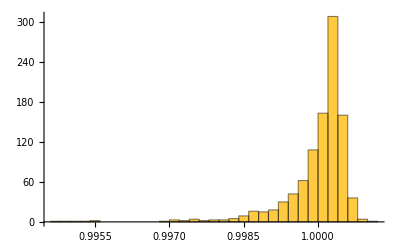

```mathematica
Histogram[normChecks,PlotRange->All]
```

```mathematica
entropies=ParallelMap[SWehrlFromRow,husimiValues];
```

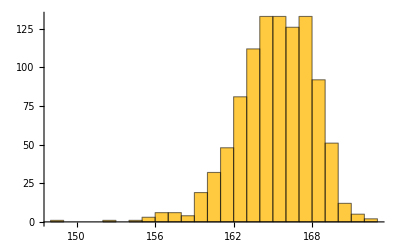

```mathematica
Histogram[entropies,PlotRange->All]
```

```mathematica
perm=Ordering[entropies];
entropiesSorted=entropies[[perm]];
eigenvecsSorted=neweigenvec[[perm]];
overlapsSorted=overlaps[[perm,All]];
husimiValuesSorted=husimiValues[[perm]];
```

```mathematica
info=SortBy[Transpose[{iprCompiled,region}],First];
```

```mathematica
newregion=info[[All,2]];
```

```mathematica
newiprs=info[[All,1]];
```

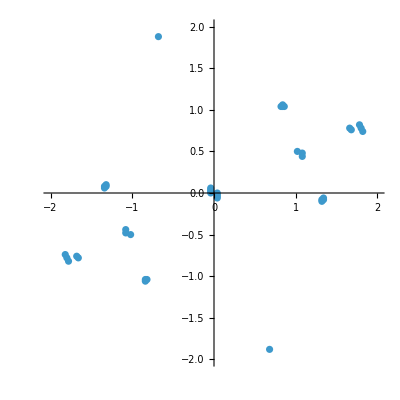

```mathematica
ListPlot[newregion[[-100;;-60]],AspectRatio->1,PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,newregion,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
```

Projecting states into Floquet basis...

```mathematica
newoverlaps=Transpose[overlaps];
```

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[i]]]^2}],PlotRange->All,Filling->Bottom,ImageSize->600,PlotLabel->Style["PR = "<>ToString[1/newiprs[[i]]],20,Black]],{i,-100,-60,1}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
plots=Table[ListPlot[Transpose[{Arg[eigenvalSorted],Abs[newoverlaps[[i]]]^2}],PlotRange->All,Filling->Bottom,ImageSize->600,PlotLabel->Style["PR = "<>ToString[1/newiprs[[i]]],20,Black]],{i,1,30,1}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

# Average energy

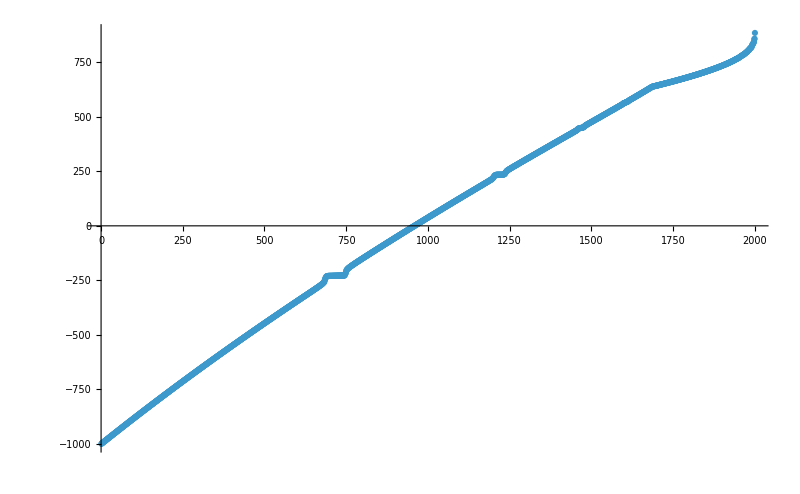

```mathematica
ListPlot[Sort[Chop[szExpectations]],PlotRange->All,ImageSize->800]
```